Update the filename here appropriately.

```mathematica
data=Import["/home/pinkpig/physics/Guth/Guth_2017/radial_sampling/spectrum.csv", "CSV"];
{k,p}=data//Transpose;
PrependTo[k,0];
PrependTo[p,p[[1]]];
```

Set the power of k that you want.

r = 5.02512563

```mathematica
kpower=2;
test=Interpolation[Transpose[{k, p*k^kpower}]]
```

InterpolatingFunction[{{0., 1000.}}, <>]

```mathematica
rv  = 5.02512563
```

rv  = 5.02512563

If kpower = 2, then the following tests the normalization of the power spectrum.

```mathematica
(16*3.141592^2)/(5.02512563
)^2*NIntegrate[test[x]*SphericalBesselJ[1,5.02512563*x]*SphericalBesselJ[1,5.02512563*x], {x, 0, Last[k]},WorkingPrecision->20, MaxRecursion->100]
```

NIntegrate::precw: The precision of the argument function (SphericalBesselJ[1,5.02513 x]^2 «1»[x]) is less than WorkingPrecision (20.).

0.00134548

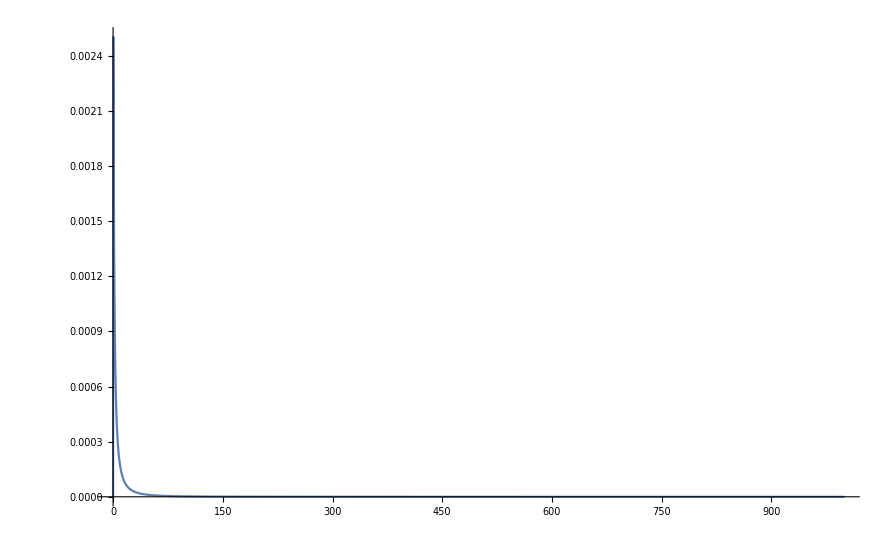

```mathematica
Plot[test[x],{x,0,Last[k]},PlotRange->All]
```